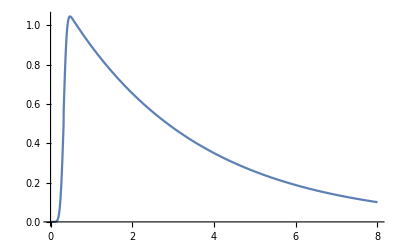

```mathematica
tr=160*^-12;
β=0.05;
t1=2 tr;
doubleExponential[t_]:=
HeavisideTheta[t1-t]Exp[-β((t-t1)/tr)]/2Erfc[Abs[t-t1]Sqrt[π]/tr]+HeavisideTheta[t-t1]Exp[-β(((t-t1)-t1)/tr)](1-1/2Erfc[(t-t1)Sqrt[π]/tr])
Plot[doubleExponential[t],{t,0,8*^-9}]
```

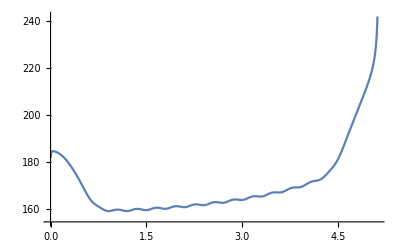

```mathematica
tSampled=Subdivide[0,20*^-9,1024];
dt=tSampled[[2]]-tSampled[[1]];
fSampled=Subdivide[0,1/dt,Length@tSampled-1];
doubleExpSampled=doubleExponential[tSampled];
doubleExpFFT=Fourier[doubleExpSampled];
ListLinePlot[
MapThread[
{#1, 20Log10[Abs[2π ⅉ#1 #2]]}&, 
{fSampled,doubleExpFFT}],
PlotRange->Full
]
```

```mathematica
+
```

```mathematica
3*^8/400*^6
```

3/4